# Dynamics of Choi matrix’s purity

## Cargar paquetes y definiciones

```mathematica
(* Establecer que el directorio sea el mismo que el de este notebook *)
SetDirectory[NotebookDirectory[]]
```

/home/jadeleon/Documents/quantum_chaotic_channels/ja_files

```mathematica
(* Cargar paquete QMB.wl *)
Get["../Mathematica_packages/"<>#]&/@{"Chaometer.wl","QMB.wl"};
```

```mathematica
labeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
unlabeledTicks=Flatten[Table[{k*j,Null},{k,2,9},{j,labeledTicks[[All,1]]}],1];
myTicks=Join[labeledTicks,unlabeledTicks];
```

## Cálculo de superoperadores del caómetro

### Parameters setup

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}(*hz=0.5 chaotic, hz=2.5 regular*)
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Three initial random states of the environment Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],5];
```

### Calculation of superoperators

```mathematica
superoperators={};
```

```mathematica
AbsoluteTiming[
Do[
AppendTo[superoperators,Superoperator[t,ψ0E[[5]],eigenvalsH,eigenvecsH,L]],
{t,10^Range[-2,2,0.08]}](* tiempos equiespaciados en escala log *)
]
```

{263.683,Null}

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_5_t_log_scale.csv",Prepend[superoperators,"L=11;{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]};SeedRandom[32371];ψ0E=Table[RandomChainProductState[L-1],3];Superoperator[t,ψ0E[[5]],eigenvalsH,eigenvecsH,L];"],"CSV"]
```

/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_5_t_log_scale.csv

### Import of superoperators

```mathematica
(* Importar los datos de los superoperadores *)
superoperators=ToExpression[Import["chaotic/superoperators_"<>ToString[#]<>"_t_log_scale.csv"][[2;;]]]&/@Range[5];
```

```mathematica
(* Calcular las matrices de Choi *)
chois=1/2*Map[Reshuffle,superoperators,{2}];
```

```mathematica
(* Calcular la pureza de las matrices de Choi *)
choisPurity=Chop[Map[Purity,chois,{2}]];
```

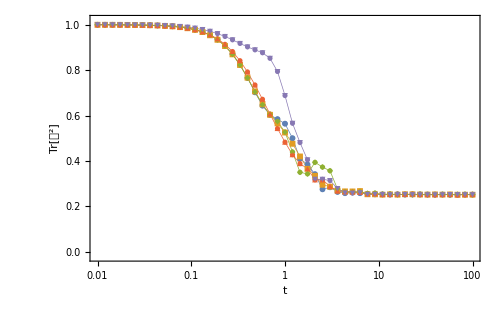

```mathematica
ListLogLinearPlot[
Transpose[{10^Range[-2,2,0.08],#}]&/@choisPurity,
PlotRange->{{10^(-2),100},{-0.02,1.02}},
Joined->True,
PlotMarkers->{Automatic,6},
PlotStyle->Directive[Thickness[0.001]],
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Automatic},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500
]
```

## Pureza con Hamiltoniano GOE

```mathematica
L=9;
```

```mathematica
(* Calcular un Hamiltoniano de GOE y obtener sus eigenvalores y eigenvectores *)
Module[{H},
H=RandomVariate[GaussianOrthogonalMatrixDistribution[2^L]];
(*U=MatrixExp[-I H];*)
{eigenvalsH,eigenvecsH}=Chop[Eigensystem[H]];
]
```

```mathematica
(* Revisar que los eigenvectores esten normalizados *)
AllTrue[Norm/@eigenvecsH,#==1.&]
```

True

```mathematica
(* Definir un estado inicial para el entorno de L-1 espines *)
(*ψ0E=VectorFromKetInComputationalBasis[{0,0,0,0}];*)
ψ0E=RandomChainProductState[L-1];
```

```mathematica
choiPurityGOE={};
```

```mathematica
(* Calcular la pureza de la matriz de Choi con eq:choi:chaometer:purity:1 *)
AppendTo[choiPurityGOE,Table[
{t,
1/4*Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,q}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]
]^2
,{i,2},{j,2},{p,2},{q,2}]}
,{t,10^Range[-3,2,0.08]}]];
```

## Comparison

```mathematica
Transpose[{10^Range[-2,2,0.08],choiPurityGOE}]
```

```mathematica
choiPurityGOE
```

{{0.01,0.963575},{0.0120226,0.947881},{0.0144544,0.925761},{0.017378,0.89494},{0.020893,0.852704},{0.0251189,0.796211},{0.0301995,0.723284},{0.0363078,0.633923},{0.0436516,0.532549},{0.0524807,0.430044},{0.0630957,0.342939},{0.0758578,0.286223},{0.0912011,0.26154},{0.109648,0.25488},{0.131826,0.252819},{0.158489,0.251582},{0.190546,0.251765},{0.229087,0.253975},{0.275423,0.255734},{0.331131,0.254328},{0.398107,0.254766},{0.47863,0.25304},{0.57544,0.253219},{0.691831,0.252851},{0.831764,0.25315},{1.,0.25119},{1.20226,0.251553},{1.44544,0.25222},{1.7378,0.253155},{2.0893,0.251032},{2.51189,0.253769},{3.01995,0.25241},{3.63078,0.253334},{4.36516,0.254516},{5.24807,0.253157},{6.30957,0.2526},{7.58578,0.254809},{9.12011,0.253579},{10.9648,0.252597},{13.1826,0.253334},{15.8489,0.254295},{19.0546,0.255094},{22.9087,0.253088},{27.5423,0.251735},{33.1131,0.251037},{39.8107,0.254766},{47.863,0.252619},{57.544,0.25307},{69.1831,0.250831},{83.1764,0.252231},{100.,0.251466}}

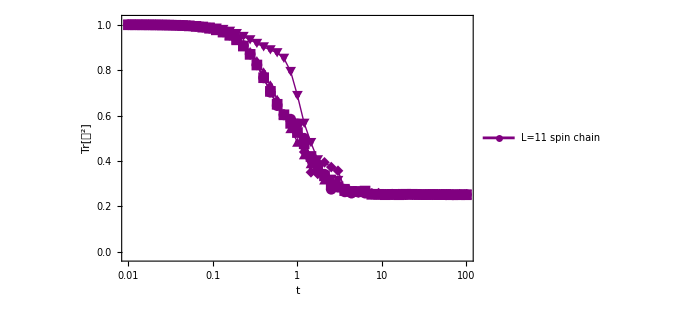

```mathematica
fig1=ListLogLinearPlot[
Transpose[{10^Range[-2,2,0.08],#}]&/@choisPurity,
PlotRange->{{10^(-2),100},{-0.02,1.02}},
Joined->True,
PlotMarkers->{Automatic,11},
PlotStyle->Directive[Purple,Thin],
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Automatic},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500,
PlotLegends->Placed[LineLegend[{ToString[TraditionalForm[HoldForm[L=11]]]<>" spin chain"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->17]], {Right,Top}]
]
```

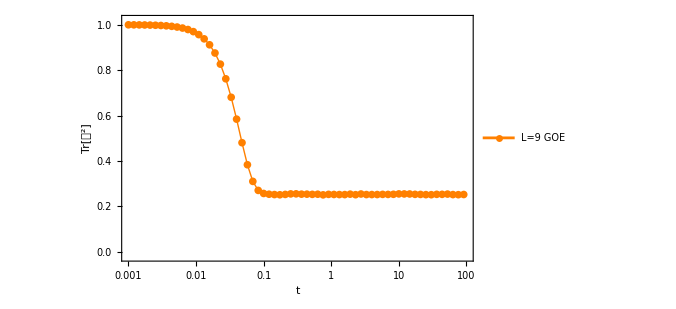

```mathematica
fig2=ListLogLinearPlot[
choiPurityGOE,
PlotRange->{{10^(-3),100},{-0.02,1.02}},
Joined->True,
PlotMarkers->{"OpenMarkers",5},
PlotStyle->Directive[Orange,Thin],
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Automatic},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500,
PlotLegends->Placed[LineLegend[{ToString[TraditionalForm[HoldForm[L=9]]]<>" GOE"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->17]], {Right,Top}]
]
```

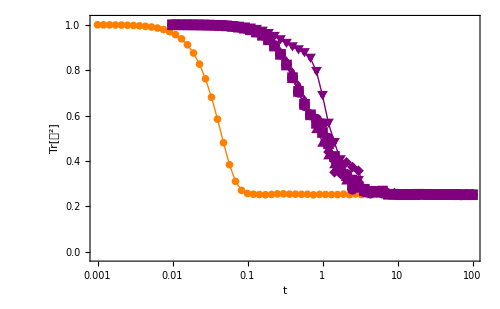

```mathematica
Show[fig2,fig1]
```